```mathematica
MKPolArea[d_,s_:100000]:=Module[{Pol,data},
Pol[n_Integer]:=Function[list,Range[n]*Transpose[{Sin[list],Cos[list]}]];
data=RandomReal[{0,2 Pi},{s,d}];
Graphics`Mesh`MeshInit[];Max@Abs@(PolygonArea/@Pol[d]/@data)]
ans=AbsoluteTiming[MKPolArea@#]&/@Range[3,200]
```

{{0.225861,4.90472},{0.231112,11.9877},{0.264914,21.7445},{0.27477,35.6494},{0.293053,57.4889},{0.312269,84.0741},{0.326132,119.063},{0.343649,156.461},{0.371366,207.883},{0.387917,256.676},{0.412811,329.689},{0.416427,403.27},{0.440094,496.458},{0.45428,629.33},{0.490043,676.837},{0.499023,784.709},{0.543591,957.62},{0.520364,1038.72},{0.55775,1225.67},{0.553625,1316.77},{0.60702,1527.4},{0.599868,1713.77},{0.641351,1958.44},{1.09408,2059.82},{0.68532,2374.67},{0.658061,2677.2},{0.693688,2843.17},{0.70323,3187.68},{0.737116,3362.78},{0.732205,3662.51},{0.778344,3902.},{0.783678,4695.54},{0.805243,4950.92},{0.791061,5148.63},{0.833769,5306.79},{0.855746,6414.53},{0.880184,6527.11},{0.873964,6522.5},{0.939365,7040.38},{0.928539,7101.88},{1.01388,8499.25},{1.04795,8031.16},{0.981706,9545.33},{1.0121,9687.26},{1.02369,10345.2},{1.025,10707.8},{1.07956,10787.5},{1.06961,11893.2},{1.08326,13203.3},{1.1052,13049.1},{1.12844,14618.3},{1.13702,14957.6},{1.14923,16897.},{1.14535,16531.6},{1.17562,16679.5},{1.2235,17087.},{1.29802,17499.3},{1.20981,18579.7},{1.25128,19329.3},{1.26576,19744.2},{1.30917,21153.5},{1.1641,21925.6},{1.20389,23286.4},{1.2072,24064.9},{1.24658,24979.5},{1.30836,27215.5},{1.27261,25825.3},{1.33228,27719.4},{1.29265,27884.4},{1.31586,30067.8},{1.33687,29469.8},{1.33576,34874.5},{1.35563,30936.9},{1.43032,31303.1},{1.38157,34804.8},{1.40347,36017.4},{1.39336,37392.9},{1.45928,39260.7},{1.43555,39378.9},{1.49076,41368.8},{1.46534,42325.5},{1.53973,43700.6},{1.48147,42681.5},{1.58395,44213.6},{1.50792,50868.5},{1.53339,48295.2},{1.67754,54437.8},{1.56899,54947.3},{1.59015,54122.},{1.60485,53314.4},{1.6242,54013.6},{1.63174,60339.7},{1.67914,60365.7},{1.66489,64768.7},{1.68132,65294.3},{1.70948,69256.4},{1.69748,68373.},{4.82729,65089.4},{5.09125,70097.5},{5.14602,67778.1},{4.81836,76177.3},{5.19798,81209.2},{5.24775,75696.5},{5.19591,75963.5},{5.22918,80792.1},{5.2872,82383.5},{4.93772,83681.6},{5.25798,86233.4},{5.15347,99129.},{5.29263,90106.9},{5.25702,99930.1},{5.29475,97693.},{5.33477,94011.},{5.44373,99785.9},{5.37028,102779.},{5.34281,103113.},{5.34325,108301.},{5.11725,110755.},{5.41328,108295.},{5.43723,107749.},{5.45804,124230.},{5.4424,110584.},{5.51836,120218.},{5.56003,127273.},{5.41075,119842.},{5.71162,121242.},{5.56777,129022.},{5.5642,138343.},{5.67978,135312.},{5.70625,140419.},{5.68991,142155.},{5.59418,144014.},{5.73184,147622.},{5.72049,142775.},{5.79354,141757.},{5.74162,150935.},{5.78783,155306.},{5.86745,163215.},{5.79742,158340.},{5.81786,160665.},{5.8124,182591.},{5.90145,172563.},{6.07921,188629.},{6.01182,205421.},{6.0372,199200.},{6.10777,181986.},{6.06332,192147.},{5.94546,202816.},{6.14309,206176.},{5.7506,200387.},{5.8802,193677.},{5.75703,214574.},{5.79981,208233.},{5.94665,209402.},{6.15218,208197.},{6.14169,229454.},{6.24955,217252.},{6.0278,238152.},{6.16868,238065.},{6.12637,221564.},{6.18925,252467.},{6.09326,240604.},{6.20809,236420.},{6.2761,242591.},{6.28796,238015.},{6.22963,248334.},{6.28322,260305.},{6.25646,252502.},{6.3377,261678.},{6.32253,256125.},{6.33143,307468.},{6.38862,279425.},{6.31944,326964.},{6.31001,274333.},{6.41794,306727.},{6.46303,334284.},{6.64925,306786.},{6.45493,326022.},{6.57538,301699.},{6.49224,320765.},{6.66848,310402.},{6.7,332094.},{6.43629,352954.},{6.43069,343893.},{6.36053,390089.},{6.29435,330403.},{6.39025,311093.},{6.52109,369802.},{6.74659,355973.},{6.6026,354511.},{6.64545,385889.},{6.76063,342276.},{6.5522,408844.},{6.74006,357698.},{6.768,360429.},{6.77395,378406.},{6.53959,426921.},{6.87664,442243.}}

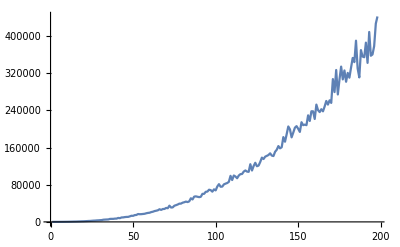

```mathematica
ListLinePlot[(Transpose@ans)[[2]]]
```